### Directory setup

```mathematica
SetDirectory["C:/Users/MaeLSTRoM/Desktop/Coding/ant/data/sleap"]
```

C:\Users\MaeLSTRoM\Desktop\Coding\ant\data\sleap

```mathematica
file=Import["testset.hdf5","Data"];
```

```mathematica
src=file⟦"/trajectory_0"⟧;
```

```mathematica
imgsize=Max[{xmax,ymax}];
scalefactor=imgsize/17.5(*pixels per cm*)
```

37.5021

### Initialize

```mathematica
list={};
Do[
src=file⟦n+Length[file]/2⟧;
frames=file⟦n⟧;
head=src⟦;;,1⟧;
thorax=src⟦;;,2⟧;
abdomen=src⟦;;,3⟧;
Do[
If[head⟦1,m⟧>1,
(*skip*),
head⟦1,m⟧=head⟦1,m-1⟧;
];
If[head⟦2,m⟧>1,
(*skip*),
head⟦2,m⟧=head⟦2,m-1⟧
]
,{m,1,Length[head⟦1⟧]}];
Do[
If[thorax⟦1,m⟧>1,
(*skip*),
thorax⟦1,m⟧=thorax⟦1,m-1⟧;
];
If[thorax⟦2,m⟧>1,
(*skip*),
thorax⟦2,m⟧=thorax⟦2,m-1⟧
]
,{m,1,Length[thorax⟦1⟧]}];
Do[
If[abdomen⟦1,m⟧>1,
(*skip*),
abdomen⟦1,m⟧=abdomen⟦1,m-1⟧;
];
If[abdomen⟦2,n⟧>1,
(*skip*),
abdomen⟦2,m⟧=abdomen⟦2,m-1⟧
]
,{m,1,Length[abdomen⟦1⟧]}];
avg=(head+thorax+abdomen)/3.;
avg=PrependTo[avg,frames];
AppendTo[list,avgᵀ];

(*Length[file] is always an even number, because the converter creates one table for trajectory and one table for frame numbers for every SLEAP trajectory in the input file.*)
,{n,1,Length[file]/2}]
```

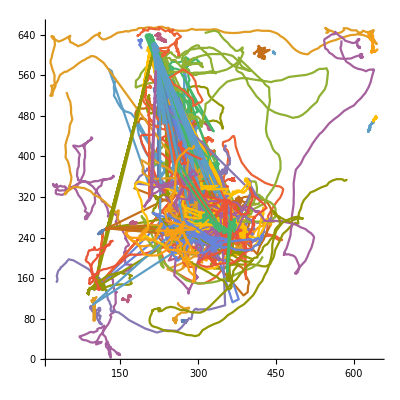

```mathematica
ListPlot[list⟦;;,;;,2;;3⟧,PlotRange->All,Joined->True,ImageSize->Full,AspectRatio->1]
```

## Jump counts/disconnect trajectories

```mathematica
Module[{jump,θ=15.1},
ct=0;
pruned={};
Do[
jump=1;
sc=0;
Do[
If[
Norm[list⟦i,j,2;;3⟧-list⟦i,j-1,2;;3⟧]>θ,
AppendTo[pruned,list⟦i,jump;;j-1⟧];
jump=j;
sc+=1;
ct+=1];
,{j,2,Length[list⟦i⟧]}];
If[sc==0,
AppendTo[pruned,list⟦i⟧];
ct+=1],
{i,1,Length[list]}]
];
```

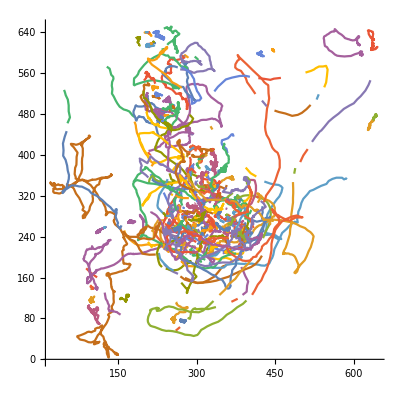

```mathematica
tr=ListPlot[pruned⟦;;,;;,2;;3⟧,PlotRange->All,Joined->True,ImageSize->Full,AspectRatio->1]
```

## Compute predicted position

```mathematica
Module[{
ω,speed,vec,dir,arg,
refrange=5(*Number of frames to refer to for finding potential next position*)
},
prediction={};
Do[
If[Length[pruned⟦n⟧]>refrange,
(*Sufficiently long trajectories*)
ω=0;
speed=0;
vec=0;
Do[
j=refrange+1-i;
vec=pruned⟦n,-j⟧-pruned⟦n,-j-1⟧;
speed+=Abs[vec];
dir=vec/(Abs[vec]+0.000000000001);
arg=dir⟦1⟧/dir⟦2⟧;
If[dir⟦2⟧≥0,
ω+=ArcTan[arg],
ω+=1.π+ArcTan[arg];
];
,{i,1,refrange}];
speed=speed/refrange;
ω=ω/refrange;
,
(*Too short to establish good prediction*)
speed=0;
ω=0;
];
AppendTo[prediction,{pruned⟦n,-1⟧,pruned⟦n,-1⟧+speed{Cos[ω],Sin[ω]}}];
,{n,1,Length[pruned]}];
]
```

```mathematica
Show[ListPlot[pruned⟦;;⟧,PlotRange->All,Joined->True,ImageSize->Full,AspectRatio->1],ListPlot[prediction⟦;;⟧,Joined->True,PlotStyle->Black]]
```

## Probability-based prediction visualized

```mathematica
position=pruned⟦37,-1,2;;3⟧;
pposition=pruned⟦37,-2,2;;3⟧;
xval=position⟦1⟧;yval=position⟦2⟧;
x1val=pposition[[1]];y1val=pposition[[2]];
initangle=OriAnt[position,pposition];
```

```mathematica
ArcCos2[300-xval,300-yval]
```

### Single step

#### Angle-only probability view

```mathematica
DensityPlot[PDF[avdist,Mod[ArcCos2[x-xval,y-yval]-initangle+π,2π]-π],{x,0,700},{y,0,700},PlotLegends->Automatic,PlotRange->Full,PlotPoints->200,MaxRecursion->5,PlotLabel->"Probability of next step angle for sample position"]
```

```mathematica
Plot[PDF[avdist,θ],{θ,-π,π},PlotRange->All]
```

#### Stepsize-only probability view

```mathematica
DensityPlot[PDF[speeddist,Sqrt[(x-xval)^2+(y-yval)^2]/scalefactor],{x,0,700},{y,0,700},PlotRange->All,PlotPoints->100,PlotLabel->"Probability of distance to next step for sample position"]
```

#### Combined probability view

```mathematica
DensityPlot[PDF[speeddist,Sqrt[(x-xval)^2+(y-yval)^2]/scalefactor]PDF[avdist,Mod[ArcCos2[x-xval,y-yval]-initangle+π,2π]-π],{x,0,700},{y,0,700},PlotRange->All,PlotPoints->100,PlotLabel->"Probability of distance to next step for sample position"]
```

```mathematica
DensityPlot[PDF[speeddist,Sqrt[(x-xval)^2+(y-yval)^2]/scalefactor]PDF[avdist,Mod[ArcCos2[x-xval,y-yval]-initangle+π,2π]-π],{x,xval-100,xval+100},{y,yval-100,yval+100},PlotRange->All,PlotPoints->50,MaxRecursion->15,PlotLabel->"Probability of distance to next step for sample position"]
```

### Two-steps

```mathematica
probrepeat=1;
dp=DensityPlot[PDF[speeddist,Sqrt[(x-xval)^2+(y-yval)^2]/(10probrepeat)]^probrepeat PDF[avdist,(Mod[ArcCos2[x-xval,y-yval]-initangle+π,2π]-π)/probrepeat]^probrepeat,{x,0,700},{y,0,700},PlotRange->All,PlotPoints->300,MaxRecursion->15,PlotLegends->Automatic,PlotLabel->"Probability of distance to next step for sample position",ImageSize->Full]
```

#### Overlay

```mathematica
Show[dp,part1,part2]
```

## Probability-based prediction compute

### Helper function

```mathematica
ArcCos2[x_,y_]:=Module[
{ans,temp,norm},
norm=Sqrt[x^2+y^2];
If[y<0,
ans=ArcCos[x/norm],
ans=-ArcCos[x/norm];
];
Return[ans]
]
```

```mathematica
OriAnt[ultim_,penultim_]:=Module[{x1,y1,x2,y2,dx,dy,norm,angle},
x1=penultim⟦1⟧;
x2=ultim⟦1⟧;
y1=penultim⟦2⟧;
y2=ultim⟦2⟧;
dx=x2-x1;
dy=y2-y1;
norm=Sqrt[dx^2+dy^2]+0.0001;
angle=ArcCos2[dx/norm,dy/norm];
Return[angle];
]
```

```mathematica
Hungarian[sources_,targets_,frags_,probs_,targetlist_]:=Module[{sourcepositions,targetpositions,size,costmatrix,invprob,boolmat,zerocount,zeros,minrow,markedzeros,markedrows,markedcolumns,unmarkedrows,unmarkedzeros,markedtotal},
sourcepositions=frags⟦sources,-1,2;;3⟧;
targetpositions=frags⟦targets,1,2;;3⟧;
size=Max[{Length[sources],Length[targets]}];

(*We want to maximize prob, so we find a quantity that can be minimized instead *)
invprob=Max[probs]-probs;

(*It is necessary to define costmatrix as square matrix first because we need a bijective mapping for linear sum assignment algorithms to work *)
costmatrix=Array[0,{size,size}];
costmatrix=Table[costmatrix⟦i,j⟧+invprob⟦sources⟦i⟧,targets⟦j⟧⟧,{i,1,size},{j,1,size}];

(*Subtract minima from each row*)
Do[costmatrix⟦i⟧=costmatrix⟦i⟧-Min[costmatrix⟦i⟧],{i,1,size}];
(*Subtract minima from each column*)
Do[costmatrix⟦;;,j⟧=costmatrix⟦;;,j⟧-Min[costmatrix⟦;;,j⟧],{j,1,size}];
(*Make an N by N boolean matrix where the zeros are marked with True and others by False*)
boolmat=Table[If[costmatrix⟦i⟧==0,True,False],{i,1,size}];
markedrows={};
(*Pick the row with fewest nonzero Trues, mark the first one and eliminate marked zero*)
While[MemberQ[Flatten@boolmat,True],
zerocount=Table[Count[boolmat⟦i⟧==True],{i,1,size}];
minrow=Min[Select[zerocount,zerocount⟦#⟧&≠0]];
zeros=Select[costmatrix⟦minrow⟧,0,1];
Table[boolmat⟦minrow,j⟧=False,{j,1,Length[zeros]}];
iwanttoeatchicken=True;

(*Remove the zeroes selected in the previous step*)
boolmat⟦minrow,;;⟧=Array[False,{size}];
Do[boolmat⟦;;,zeros⟦i⟧⟧=Array[False,{size}];
markedzeros=AppendTo[markedrows,{minrow,zeros⟦i⟧}],{i,1,size}]];
markedrows=markedzeros⟦;;,1⟧;
unmarkedrows=Select[Range[size],!MemberQ[markedrows]];
Do[markedcolumns=Select[Range[size],costmatrix⟦i,#⟧&==0],{i,1,Length[unmarkedrows]}];

(*Check the total number of marked rows and columns*)
markedtotal=Length[markedrows]+Length[markedcolumns];

If[markedtotal==size,
(*If it matches the size of the matrix, proceed with assignment*),
(*If it does not match the size of matrix, modify matrix until it does*)
]
]
```

### Obtain probabilities

```mathematica
Module[{selected,selecteds,ultim,penultim,orientation,prob,probs,nsteps},
probs={};
selecteds={};
ct=0;
Do[
probs=AppendTo[probs,{}];
selecteds=AppendTo[selecteds,{}];
If[Length[pruned⟦n⟧]>1,
penultim=pruned⟦n,-2⟧;
ultim=pruned⟦n,-1⟧;
orientation=OriAnt[ultim,penultim];
Do[
prob={};
selected=Select[pruned,#⟦1,1⟧==t&];
Do[nsteps=t-Max[pruned⟦n,-1,1⟧];
prob=AppendTo[prob,PDF[speeddist,Sqrt[(selected⟦m,1,2⟧-ultim⟦2⟧)^2+(selected⟦m,1,3⟧-ultim⟦3⟧)^2]/(10nsteps)]^nsteps
PDF[avdist,1/nsteps(Mod[ArcCos2[(selected⟦m,1,2⟧-ultim⟦2⟧)/100,(selected⟦m,1,3⟧-ultim⟦3⟧)/100]-orientation+π,2π]-π)]^nsteps ];
,{m,1,Length[selected]}];
probs⟦-1⟧=AppendTo[probs⟦-1⟧,prob];
selecteds⟦-1⟧=AppendTo[selecteds⟦-1⟧,selected];
,{t,Max[pruned⟦n,-1,1⟧]+1,Max[pruned⟦n,-1,1⟧]+11}]]
,{n,1,Length[pruned]}];
probsout=probs;
selectedout=selecteds;
]
```

### Join trajectories

#### Pick maximum

```mathematica
Module[{source,target,linklabel,linked},
(*
algorithm:
 1. Iterate through each frame
2. At the given frame, look for all trajectories that end at that time.
3. At the subsequent frame, look for all trajectories that begin at that time.
4. For each target, find the source that has best likelihood for the target.
5. Repeat until all targets are assigned.
6. Proceed to the next frame, carrying over any unmatched trajectory from previous frame.
7. If a trajectory termination point goes unmatched for longer than 5 frames, remove it from the trajectories.
*)
source={};
target={};
Do[
Do[
If[pruned⟦n,-1,1⟧==t,
AppendTo[source,n]
];
If[pruned⟦n,1,1⟧==t,
AppendTo[target,n]
],{n,1,Length[pruned]}];
Hungarian[source,target,pruned,probsout,selectedout];
,{t,1,Length[frames]}];
]
```

```mathematica
Length[selectedout]
```

663

```mathematica
Length[pruned]
```